```mathematica
Needs["PlotLegends`"]
```

```mathematica
SetDirectory["~/jennaproject/data"]
```

/Users/Jenna/jennaproject/data

```mathematica
filelist0=Import["~/jennaproject/data/alpha_files.txt","List"];
filelistn1=Import["~/jennaproject/data/alphafilesn1.txt","List"];
filelistn2=Import["~/jennaproject/data/alphafilesn2.txt","List"];
filelistp1=Import["~/jennaproject/data/alphafilesp1.txt","List"];
filelistp2=Import["~/jennaproject/data/alphafilesp2.txt","List"];
```

```mathematica
bfiles=Import[filelist0[[#]],"Table"]&/@Range[1,Dimensions[filelist0][[1]]];
bfilesn1=Import[filelistn1[[#]],"Table"]&/@Range[1,Dimensions[filelistn1][[1]]];
bfilesn2=Import[filelistn2[[#]],"Table"]&/@Range[1,Dimensions[filelistn2][[1]]];
bfilesp1=Import[filelistp1[[#]],"Table"]&/@Range[1,Dimensions[filelistp1][[1]]];
bfilesp2=Import[filelistp2[[#]],"Table"]&/@Range[1,Dimensions[filelistp2][[1]]];
```

```mathematica
bfile0=Import["~/jennaproject/data/alpha_b2_0.0_br_0.000.txt","Table"];
bfile0n1=Import["~/jennaproject/data/alpha_b2_-0.1_br_0.000.txt","Table"];
bfile0n2=Import["~/jennaproject/data/alpha_b2_-0.2_br_0.000.txt","Table"];
bfile0p1=Import["~/jennaproject/data/alpha_b2_0.1_br_0.000.txt","Table"];
bfile0p2=Import["~/jennaproject/data/alpha_b2_0.2_br_0.000.txt","Table"];
```

```mathematica
Dimensions[bfiles]
```

{20,11,3}

```mathematica
bpts=Mean[bfiles[[#,All,1]]]&/@Range[1,Dimensions[bfiles][[1]]];
bptsn1=Mean[bfilesn1[[#,All,1]]]&/@Range[1,Dimensions[bfilesn1][[1]]];
bptsn2=Mean[bfilesn2[[#,All,1]]]&/@Range[1,Dimensions[bfilesn2][[1]]];
bptsp1=Mean[bfilesp1[[#,All,1]]]&/@Range[1,Dimensions[bfilesp1][[1]]];
bptsp2=Mean[bfilesp2[[#,All,1]]]&/@Range[1,Dimensions[bfilesp2][[1]]];
```

```mathematica
bvals=Range[0.001,0.02,0.001];
```

```mathematica
mark1=Graphics[{Blue,Disk[]}];
mark2=Graphics[{Red,Disk[]}];
mark3=Graphics[{Orange,Disk[]}];
mark4=Graphics[{Green,Disk[]}];
mark5=Graphics[{Purple,Disk[]}];
```

```mathematica
α=ListLogLinearPlot[{bvals,-bpts+Mean[bfile0[[All,1]]]}ᵀ,PlotMarkers-> {mark1, .025},PlotLegend->{"b2 = 0.0"}];
β=ListLogLinearPlot[{bvals,-bptsn1+Mean[bfile0n1[[All,1]]]}ᵀ,PlotMarkers-> {mark2, .025},PlotLegend->{"b2 = -0.1"}];
γ=ListLogLinearPlot[{bvals,-bptsp1+Mean[bfile0p1[[All,1]]]}ᵀ,PlotMarkers-> {mark3, .025},PlotLegend->{"b2 = 0.1"}];
δ=ListLogLinearPlot[{bvals,-bptsp2+Mean[bfile0p2[[All,1]]]}ᵀ,PlotMarkers-> {mark4, .025},PlotLegend->{"b2 = 0.2"}];
ϵ=ListLogLinearPlot[{bvals,-bptsn2+Mean[bfile0n2[[All,1]]]}ᵀ,PlotMarkers-> {mark5, .025},PlotLegend->{"b2 = -0.2"}];
```

```mathematica
-bptsn2+Mean[bfile0n2[[All,1]]]
```

{0.000167069,0.000329844,0.000488334,0.000642526,0.000792422,0.000938006,0.00107927,0.00121619,0.00134875,0.00147691,0.00160065,0.00171993,0.0018347,0.00194488,0.00205038,0.00215084,0.00224386,0.00277589,0.00284093,0.00290202}

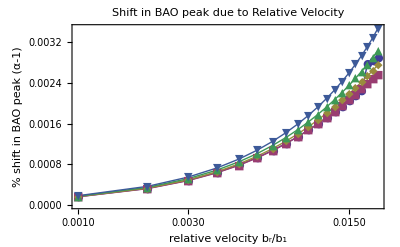

```mathematica
ListLogLinearPlot[{{bvals,-bptsn2+Mean[bfile0n2[[All,1]]]}ᵀ,{bvals,-bptsn1+Mean[bfile0n1[[All,1]]]}ᵀ,{bvals,-bpts+Mean[bfile0[[All,1]]]}ᵀ,{bvals,-bptsp1+Mean[bfile0p1[[All,1]]]}ᵀ,{bvals,-bptsp2+Mean[bfile0p2[[All,1]]]}ᵀ},PlotMarkers-> {Automatic,Medium},PlotLegend->{Style["b2 = -0.2",18],Style["b2 = -0.1",18],Style["b2 = 0.0",18],Style["b2 = 0.1",18],Style["b2 = 0.2",18]},LegendShadow->None,LegendPosition->{-0.7,-0.3},Joined->True,PlotStyle->Thick,BaseStyle->{FontSize->18},Frame->True, FrameLabel->{"relative velocity b_r/b_1","% shift in BAO peak (α-1)"},RotateLabel->True,PlotLabel->"Shift in BAO peak due to Relative Velocity"]
```